```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,3.,4.,5.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,150.,200.,250.,300.,350.,400.,450.,500.,600.,700.,800.,900.,1000.,1050.,1100.,1150.,1200.,1250.,1300.,1350.,1400.,1450.,1500.,1550.,5000.},{x,-1,-0.5,0.,0.5,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->80(*,AccuracyGoal->10,PrecisionGoal->10*),WorkingPrecision->12];
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->100])-(Nc h^2 mf2[h,ρ])/(16 π^2);
gamma2[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]-gammavac[p0,ps,ρ0,h,Mmass,MZ];
λ300=75.8;
ν300=-482.^2;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

## Finite T

```mathematica
fpi=Flatten[Import["./sigmamu320T.dat"]];
T=Flatten[Import["./T.dat"]];
```

```mathematica
ET=ParallelTable[FindMinimum[{gamma2[0.,ps,fpi[[j]]^2/2,92.57845450044942^2/2,6.5,T[[j]],320.,300.,300.]+(0.)^2+(ps)^2+(λ300 fpi[[j]]^2/2+ν300)},{ps,210},WorkingPrecision->15,AccuracyGoal->15,PrecisionGoal->15][[2]][[1]][[2]]//Quiet,{j,1,80,1}];
```

```mathematica
mf=Table[√mf2[6.5,fpi[[i]]^2/2],{i,1,80,1}]
```

{60.0691,60.0585,60.0591,60.0508,60.0364,60.0181,59.9961,59.9701,59.9403,59.9067,59.8693,59.8281,59.7831,59.7344,59.6819,59.6258,59.5659,59.5024,59.4353,59.3645,59.2902,59.2124,59.131,59.0462,58.9579,58.8663,58.7712,58.6729,58.5713,58.4665,58.3584,58.2473,58.133,58.0156,57.8953,57.7719,57.6457,57.5165,57.3846,57.2499,57.1124,56.9723,56.8295,56.6842,56.5364,56.3861,56.2333,56.0782,55.9208,55.7611,55.5992,55.4351,55.269,55.1008,54.9305,54.7583,54.5843,54.4084,54.2306,54.0512,53.87,53.6872,53.5028,53.3169,53.1295,52.9407,52.7504,52.5588,52.366,52.1719,51.9766,51.7801,51.5826,51.384,51.1844,50.9838,50.7823,50.5799,50.3768,50.1728}

```mathematica
pfermi=√(320^2-mf^2)
```

{314.311,314.313,314.313,314.315,314.318,314.321,314.325,314.33,314.336,314.342,314.35,314.357,314.366,314.375,314.385,314.396,314.407,314.419,314.432,314.445,314.459,314.474,314.489,314.505,314.522,314.539,314.557,314.575,314.594,314.614,314.634,314.654,314.675,314.697,314.719,314.742,314.765,314.789,314.813,314.837,314.862,314.888,314.913,314.94,314.966,314.993,315.02,315.048,315.076,315.104,315.133,315.162,315.191,315.22,315.25,315.28,315.31,315.341,315.371,315.402,315.433,315.464,315.496,315.527,315.559,315.59,315.622,315.654,315.686,315.718,315.751,315.783,315.815,315.848,315.88,315.912,315.945,315.977,316.01,316.042}

```mathematica
T1=Table[T[[i]],{i,1,80,1}]
```

{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6,8.1,8.6,9.1,9.6,10.1,10.6,11.1,11.6,12.1,12.6,13.1,13.6,14.1,14.6,15.1,15.6,16.1,16.6,17.1,17.6,18.1,18.6,19.1,19.6,20.1,20.6,21.1,21.6,22.1,22.6,23.1,23.6,24.1,24.6,25.1,25.6,26.1,26.6,27.1,27.6,28.1,28.6,29.1,29.6,30.1,30.6,31.1,31.6,32.1,32.6,33.1,33.6,34.1,34.6,35.1,35.6,36.1,36.6,37.1,37.6,38.1,38.6,39.1,39.6}

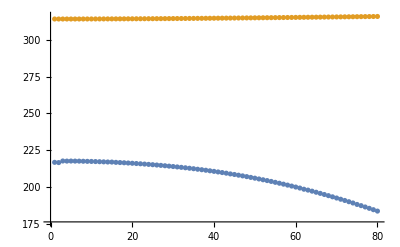

```mathematica
ListPlot[{ET,pfermi}]
```

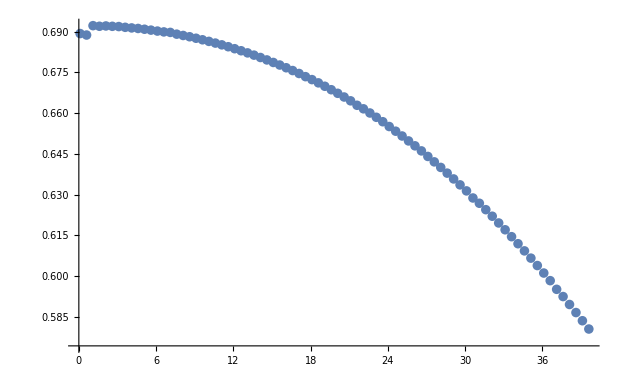

```mathematica
ListPlot[Transpose[{T1,ET/pfermi}]]
```

```mathematica
Export["pF.dat",pfermi]
Export["pmin.dat",ET]
```

pF.dat

pmin.dat

```mathematica
Export["T1.dat",T1]
```

T1.dat

```mathematica
ET1=Table[ParallelTable[gamma2[0.,ps,fpi[[j]]^2/2,6.5,T[[j]],320.,300.,300.]+(0.)^2+(ps)^2+(λ300 fpi[[j]]^2/2+ν300),{ps,280.,360.,2}],{j,1,1,1}];
```

Limit::ivar: 308. is not a valid variable.

Limit::ivar: 320. is not a valid variable.

Limit::ivar: 280. is not a valid variable.

Limit::ivar: 292. is not a valid variable.

Limit::ivar: 296. is not a valid variable.

Limit::ivar: 322. is not a valid variable.

Limit::ivar: 284. is not a valid variable.

Limit::ivar: 288. is not a valid variable.

Limit::ivar: 300. is not a valid variable.

Limit::ivar: 302. is not a valid variable.

Limit::ivar: 304. is not a valid variable.

Limit::ivar: 306. is not a valid variable.

Limit::ivar: 310. is not a valid variable.

Limit::ivar: 312. is not a valid variable.

Limit::ivar: 314. is not a valid variable.

Limit::ivar: 316. is not a valid variable.

Limit::ivar: 318. is not a valid variable.

Limit::ivar: 324. is not a valid variable.

Limit::ivar: 282. is not a valid variable.

Limit::ivar: 294. is not a valid variable.

Limit::ivar: 298. is not a valid variable.

Limit::ivar: 326. is not a valid variable.

Limit::ivar: 328. is not a valid variable.

Limit::ivar: 286. is not a valid variable.

Limit::ivar: 290. is not a valid variable.

Limit::ivar: 330. is not a valid variable.

Limit::ivar: 332. is not a valid variable.

Limit::ivar: 334. is not a valid variable.

Limit::ivar: 336. is not a valid variable.

Limit::ivar: 338. is not a valid variable.

Limit::ivar: 340. is not a valid variable.

Limit::ivar: 342. is not a valid variable.

Limit::ivar: 344. is not a valid variable.

Limit::ivar: 346. is not a valid variable.

Limit::ivar: 348. is not a valid variable.

Limit::ivar: 350. is not a valid variable.

Limit::ivar: 352. is not a valid variable.

Limit::ivar: 354. is not a valid variable.

Limit::ivar: 356. is not a valid variable.

Limit::ivar: 358. is not a valid variable.

Limit::ivar: 360. is not a valid variable.

Limit::ivar: 280. 不是一个有效的变量.

Limit::ivar: 282. 不是一个有效的变量.

Limit::ivar: 284. 不是一个有效的变量.

General::stop: 在本次计算中，Limit::ivar 的进一步输出将被抑制.

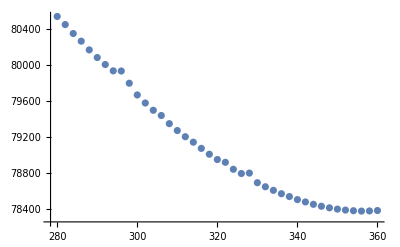

Limit::ivar: 280. 不是一个有效的变量.

Limit::ivar: 282. 不是一个有效的变量.

Limit::ivar: 284. 不是一个有效的变量.

General::stop: 在本次计算中，Limit::ivar 的进一步输出将被抑制.

-Graphics-

```mathematica
ListPlot[Transpose[{Flatten[Table[i,{i,280,360,2}]],Flatten[ET1]}]]
```